```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

```mathematica
NL=256;(*格子数*)
L=10^-12;(*物理的ボックスサイズ in Mpc*)
npeak=16;(*パワースペクトルのピーク波数*)
kpeak=(2π npeak)/NL
```

π/8

```mathematica
(*乱数シード, Subscript[μ̂, 2], Subscript[k̂, 3], k_*Subscript[r, m], Subscript[ζ, m], Subscript[C, m] (あるいは Subscript[C̄, m]), ln W, ピーク位置の x, y, z が出力されている想定. 自分のデータに応じて適宜修正*)
SamplingData=Import["probabilities_recenter.dat"];
Ntot=Length[SamplingData](*サンプリング数*)
```

10000

```mathematica
Cth=2/5;(*0.533;*)(*平均コンパクションを使ってるなら 0.4*)
```

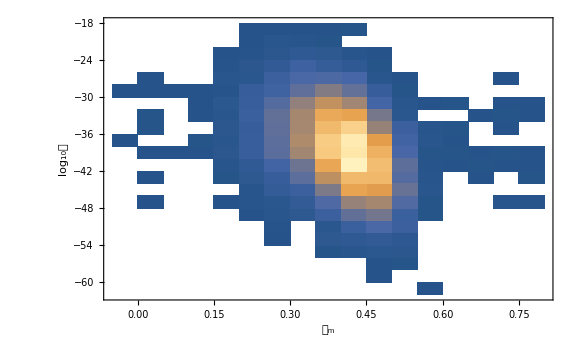

```mathematica
DensityHistogram[Map[{#[[6]],Log10[Exp[#[[7]]]]}&,SamplingData],FrameLabel->{Subscript[𝒞, "m"],"log_10𝒲"},GridLines->{{Cth},None}]
```

```mathematica
MPBH[xm_,zetam_,Cm_]=xm^2 E^(2zetam)(Cm-Cth)^γ/.{γ->0.36};(*Subscript[M, PBH]/M_(k_*)*)
```

```mathematica
Mks=(NL/L kpeak/(1.56 10^13))^-2(*M_(k_*) in 10^20 g*)
```

0.0240796

```mathematica
MPBHList=Map[{#[[3]],MPBH[#[[4]],#[[5]],#[[6]]]Mks,#[[7]],Max[Abs[#[[8;;10]]]]}&,Select[SamplingData,#[[6]]>Cth&]];(*Subscript[k̂, 3], MPBH / 10^20 g, lnW, Max[peak の |x|,|y|,|z|]*)
```

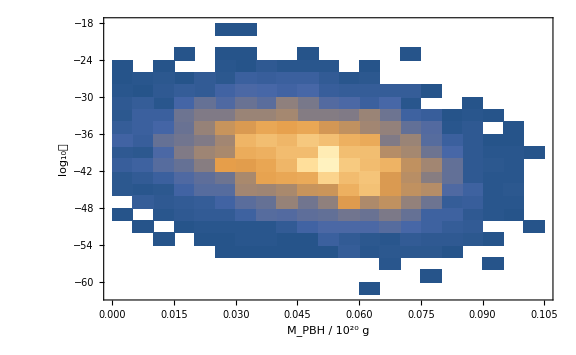

```mathematica
DensityHistogram[Map[{#[[1]],Log10[Exp[#[[2]]]]}&,MPBHList[[All,2;;3]]],FrameLabel->{"M_PBH / 10^20 g","log_10𝒲"}]
```

```mathematica
DlnM=HistogramList[Log[MPBHList[[All,2]]]][[1,2]]-HistogramList[Log[MPBHList[[All,2]]]][[1,1]](*ヒストグラム lnM のビン幅*)
```

1/10

```mathematica
lnMmin=HistogramList[Log[MPBHList[[All,2]]]][[1,1]](*ヒストグラム lnM の最小値*)
lnMmax=HistogramList[Log[MPBHList[[All,2]]]][[1]]//Last(*ヒストグラム lnM の最大値*)
```

-69/10

-11/5

```mathematica
lnMbinning[lnM_,m_]:=Select[MPBHList,(lnM<=Log[#[[2]]]<lnM+DlnM&&#[[1]]>-5&&#[[4]]<=m)&];(*ビンに入り, m ボックスに入るデータを選ぶ*)
k33sumlnM[lnM_,m_]:=Total[(lnMbinning[lnM,m][[All,1]])^3](*ビン内で Subscript[k̂, 3]^3 の総和を求める*)
```

```mathematica
mmax=5;
```

```mathematica
nSlnMk3List=Table[{lnM+DlnM/2,k33sumlnM[lnM,mmax]/(Ntot DlnM)},{lnM,lnMmin,lnMmax,DlnM}];(*Subscript[k̂, 3]^3 重みを採用した MPBH の数密度*)
nSlnMboxList[m_]:=Table[{lnM+DlnM/2,Length[lnMbinning[lnM,m]]/(Ntot DlnM (2m+1)^2)},{lnM,lnMmin,lnMmax,DlnM}];(*m ボックス重みを採用した MPBH の数密度*)
```

```mathematica
wlnMList[m_]:=Table[{lnM,If[Length[lnMbinning[lnM,m]]>1,Exp[Mean[lnMbinning[lnM,m][[All,3]]]+Variance[lnMbinning[lnM,m][[All,3]]]/2],0]},{lnM,lnMmin,lnMmax,DlnM}];(*各ビンの W の平均値*)
wlnMerrp[m_]:=Table[{lnM,If[Length[lnMbinning[lnM,m]]>1,Abs[Exp[Sqrt[Variance[lnMbinning[lnM,m][[All,3]]]/Length[lnMbinning[lnM,m]]+Variance[lnMbinning[lnM,m][[All,3]]]^2/(2Length[lnMbinning[lnM,m]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];(*W の上方誤差*)
wlnMerrm[m_]:=Table[{lnM,If[Length[lnMbinning[lnM,m]]>1,Abs[Exp[-Sqrt[Variance[lnMbinning[lnM,m][[All,3]]]/Length[lnMbinning[lnM,m]]+Variance[lnMbinning[lnM,m][[All,3]]]^2/(2Length[lnMbinning[lnM,m]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];(*W の下方誤差*)
```

```mathematica
nTlnMk3List=ParallelTable[{nSlnMk3List[[i,1]]//Exp,nSlnMk3List[[i,2]]wlnMList[mmax][[i,2]]Around[1,{wlnMerrm[mmax][[i,2]],wlnMerrp[mmax][[i,2]]}]},{i,Length[nSlnMk3List]}];(*Subscript[k̂, 3]^3 重みを採用した真の数密度*)
nTlnMboxList[m_]:=ParallelTable[{nSlnMboxList[m][[i,1]]//Exp,nSlnMboxList[m][[i,2]]wlnMList[m][[i,2]]Around[1,{wlnMerrm[m][[i,2]],wlnMerrp[m][[i,2]]}]},{i,Length[nSlnMboxList[m]]}];(*m ボックス重みを採用した真の数密度*)
```

```mathematica
AbsoluteTiming[
fPBHk3=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMk3List];(*Subscript[k̂, 3]^3 重みを採用した fPBH のリスト*)
fPBHbox0=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMboxList[0]];(*0 ボックス重みを採用した fPBH のリスト*)
fPBHbox1=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMboxList[1]];(*1 ボックス重みを採用した fPBH のリスト*)
fPBHbox2=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMboxList[2]];(*2 ボックス重みを採用した fPBH のリスト*)
fPBHbox3=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMboxList[3]];(*3 ボックス重みを採用した fPBH のリスト*)
fPBHbox4=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMboxList[4]];(*4 ボックス重みを採用した fPBH のリスト*)
fPBHbox5=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMboxList[5]];(*5 ボックス重みを採用した fPBH のリスト*)
]
```

{133.283,Null}

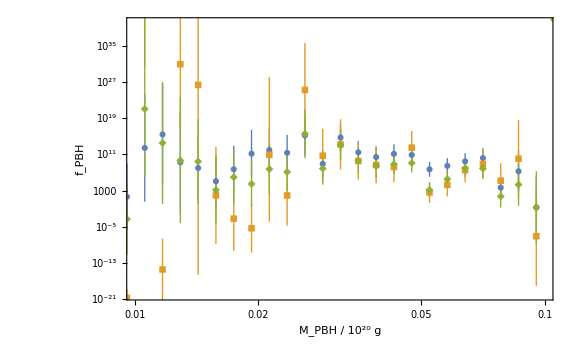

```mathematica
ListLogLogPlot[{fPBHk3(*,fPBHbox0*),fPBHbox1,fPBHbox2(*,fPBHbox3,fPBHbox4,fPBHbox5*)},Joined->False,FrameLabel->{"M_PBH / 10^20 g",Subscript[f, PBH]},PlotRange->{{0.01,0.1},{10^-20,10^40}},PlotMarkers->Automatic]
```

```mathematica
ListLogLogPlot[{fPBHk3(*,fPBHbox0*),fPBHbox1,fPBHbox2(*,fPBHbox3,fPBHbox4,fPBHbox5*)},Joined->False,FrameLabel->{"M_PBH / 10^20 g",Subscript[f, PBH]},PlotRange->{{0.01,0.1},{10^-20,10^40}},PlotMarkers->Automatic]
```

-Graphics-

```mathematica
ResourceFunction["PlotGrid"][{{ListLogLogPlot[fPBHk3,Joined->False,FrameLabel->{{Subscript[f, PBH],None},{"M_PBH / 10^20 g",Subscript[k̂, 3]^3}},PlotRange->{{0.01,0.1},{10^-20,10^40}},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],ListLogLogPlot[fPBHbox1,Joined->False,FrameLabel->{{Subscript[f, PBH],None},{"M_PBH / 10^20 g",m==1}},PlotRange->{{0.01,0.1},{10^-20,10^40}},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],ListLogLogPlot[fPBHbox2,Joined->False,FrameLabel->{{Subscript[f, PBH],None},{"M_PBH / 10^20 g",m==2}},PlotRange->{{0.01,0.1},{10^-20,10^40}},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]]}}]
```

-Graphics-

```mathematica
nTlnMk3noE=ParallelTable[{nSlnMk3List[[i,1]]//Exp,nSlnMk3List[[i,2]]wlnMList[mmax][[i,2]]},{i,Length[nSlnMk3List]}];(*Subscript[k̂, 3]^3 重みを採用した真の数密度*)
nTlnMboxnoE[m_]:=ParallelTable[{nSlnMboxList[m][[i,1]]//Exp,nSlnMboxList[m][[i,2]]wlnMList[m][[i,2]]},{i,Length[nSlnMboxList[m]]}];(*m ボックス重みを採用した真の数密度*)
```

```mathematica
AbsoluteTiming[
fPBHk3noE=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMk3noE];(*Subscript[k̂, 3]^3 重みを採用した fPBH のリスト*)
fPBHbox0noE=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMboxnoE[0]];(*0 ボックス重みを採用した fPBH のリスト*)
fPBHbox1noE=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMboxnoE[1]];(*1 ボックス重みを採用した fPBH のリスト*)
fPBHbox2noE=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMboxnoE[2]];(*2 ボックス重みを採用した fPBH のリスト*)
fPBHbox3noE=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMboxnoE[3]];(*3 ボックス重みを採用した fPBH のリスト*)
fPBHbox4noE=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMboxnoE[4]];(*4 ボックス重みを採用した fPBH のリスト*)
fPBHbox5noE=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMboxnoE[5]];(*5 ボックス重みを採用した fPBH のリスト*)
]
```

{51.897,Null}

```mathematica
Mmin=0.03;
Mmax=0.1;
Total[Select[fPBHk3noE,Mmax>#[[1]]>Mmin&][[All,2]]]DlnM
Total[Select[fPBHbox0noE,Mmax>#[[1]]>Mmin&][[All,2]]]DlnM
Total[Select[fPBHbox1noE,Mmax>#[[1]]>Mmin&][[All,2]]]DlnM
Total[Select[fPBHbox2noE,Mmax>#[[1]]>Mmin&][[All,2]]]DlnM
Total[Select[fPBHbox3noE,Mmax>#[[1]]>Mmin&][[All,2]]]DlnM
Total[Select[fPBHbox4noE,Mmax>#[[1]]>Mmin&][[All,2]]]DlnM
Total[Select[fPBHbox5noE,Mmax>#[[1]]>Mmin&][[All,2]]]DlnM
```

5.19315×10^13

3.7285×10^30

1.85609×10^12

1.10649×10^12

2.77458×10^11

6.41346×10^10

4.29331×10^10